```mathematica
test[var1_,var2_,var3_,var4_,var5_]:=Module[{Dd=var1,Du=var2,χ1=var3,χ2=var4,Tmax=var5},L=900;slope=0.0;sigma=10;
scaling=0.1;
shift=0;
sol=NDSolve[{
D[ρ[x,t],t]==Dd*D[ρ[x,t],x,x]-D[χ1*ρ[x,t]*D[c[x,t],x]/(c[x,t]),x],
D[c[x,t],t]==D[c[x,t],x,x]-c[x,t]*ρ[x,t],
D[u[x,t],t]==Du*D[u[x,t],x,x]-D[χ2*u[x,t]*D[c[x,t],x]/(c[x,t]),x],

u[x,0]==scaling*Exp[-(x-shift)^2/(2*sigma^2)],ρ[x,0]==scaling*Exp[-(x-shift)^2/(2*sigma^2)],c[x,0]==1,
Derivative[1,0][c][0,t]==slope,Derivative[1,0][u][0,t]==D[scaling*Exp[-(x-shift)^2/(2*sigma^2)],x]/.x->0,Derivative[1,0][ρ][0,t]==D[scaling*Exp[-(x-shift)^2/(2*sigma^2)],x]/.x->0,
Derivative[1,0][c][L,t]==0,Derivative[1,0][u][L,t]==0,Derivative[1,0][ρ][L,t]==0
},{c,ρ,u},{x,0,L},{t,0,Tmax},MaxStepSize->1];sol]
```

```mathematica
z1=test[0.07,0.2,0.2,0.24,10000];
```

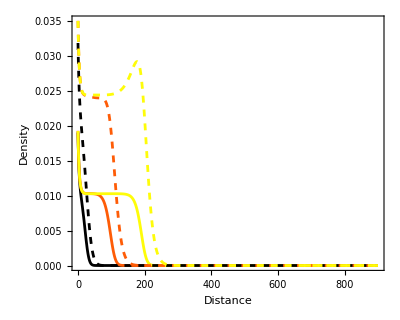

```mathematica
(*Plot consumer and sensor populations*)
colors=ColorData[3,"ColorList"];
p1=Plot[{ρ[x,1000]/.z1,ρ[x,5000]/.z1,ρ[x,10000]/.z1},{x,0,L},PlotRange->{{0,L/2},{0,All}},PlotStyle->colors,PlotLegends->Placed[{"Consumer",None,None},{0.8,0.8}],AspectRatio->0.8];
p2=Plot[{u[x,1000]/.z1,u[x,5000]/.z1,u[x,10000]/.z1},{x,0,L},PlotRange->{{0,L/2},{0,All}},PlotStyle->Partition[Riffle[colors,Dashed],2],PlotLegends->Placed[{"Sensor",None,None},{0.8,0.8}],AspectRatio->0.8];
plt=Show[p1,p2,Frame->True,FrameLabel->{"Distance","Density"},BaseStyle->{FontSize->12}]
```

```mathematica
(*Traveling wave profiles with a shifted Gaussian initial density*)
```

```mathematica
test[var1_,var2_,var3_,var4_,var5_]:=Module[{Dd=var1,Du=var2,χ1=var3,χ2=var4,Tmax=var5},L=900;slope=0.0;sigma=10;
scaling=0.1;
shift=-3;
sol=NDSolve[{
D[ρ[x,t],t]==Dd*D[ρ[x,t],x,x]-D[χ1*ρ[x,t]*D[c[x,t],x]/(c[x,t]),x],
D[c[x,t],t]==D[c[x,t],x,x]-c[x,t]*ρ[x,t],
D[u[x,t],t]==Du*D[u[x,t],x,x]-D[χ2*u[x,t]*D[c[x,t],x]/(c[x,t]),x],

u[x,0]==scaling*Exp[-(x-shift)^2/(2*sigma^2)]+scaling*(1-Exp[-(0-shift)^2/(2*sigma^2)]),ρ[x,0]==scaling*Exp[-(x-shift)^2/(2*sigma^2)]+scaling*(1-Exp[-(0-shift)^2/(2*sigma^2)]),c[x,0]==1,
Derivative[1,0][c][0,t]==slope,Derivative[1,0][u][0,t]==D[scaling*Exp[-(x-shift)^2/(2*sigma^2)],x]/.x->0,Derivative[1,0][ρ][0,t]==D[scaling*Exp[-(x-shift)^2/(2*sigma^2)],x]/.x->0,
Derivative[1,0][c][L,t]==0,Derivative[1,0][u][L,t]==0,Derivative[1,0][ρ][L,t]==0
},{c,ρ,u},{x,0,L},{t,0,Tmax},MaxStepSize->1];sol]
```

```mathematica
z1=test[0.07,0.2,0.2,0.24,10000];
```

$Aborted

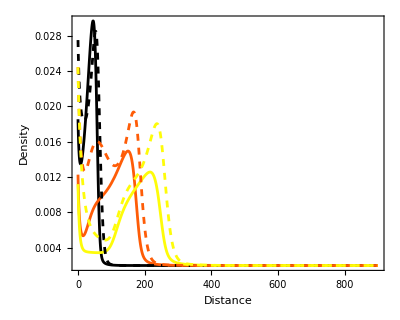

```mathematica
(*Plot consumer and sensor populations*)
colors=ColorData[3,"ColorList"];
p1=Plot[{ρ[x,5000]/.z1,ρ[x,10000]/.z1,ρ[x,15000]/.z1},{x,0,L},PlotRange->{{0,L/2},{0,All}},PlotStyle->colors,PlotLegends->Placed[{"Consumer",None,None},{0.8,0.8}],AspectRatio->0.8];
p2=Plot[{u[x,5000]/.z1,u[x,10000]/.z1,u[x,15000]/.z1},{x,0,L},PlotRange->{{0,L/2},{0,All}},PlotStyle->Partition[Riffle[colors,Dashed],2],PlotLegends->Placed[{"Sensor",None,None},{0.8,0.8}],AspectRatio->0.8];
plt=Show[p1,p2,Frame->True,FrameLabel->{"Distance","Density"},BaseStyle->{FontSize->12}]
```

```mathematica
shift=-3;
scaling=0.1;
N[D[scaling*Exp[-(x-shift)^2/(2*sigma^2)],x]/.x->0]
```

-0.00286799

```mathematica
scaling=0.1;
shift=-2;
0.1-scaling*Exp[-(0-shift)^2/(2*sigma^2)]
```

0.00198013